# Working through the chapter Combinatorial Searching in Knuth’s TAOCP

## Exercise 41

For what integers n do we have K_n=P_n? K_n=C_n?




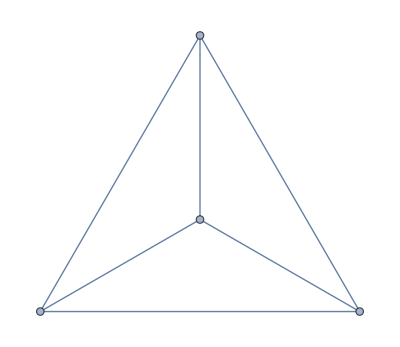

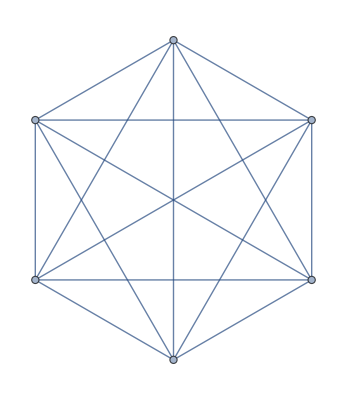
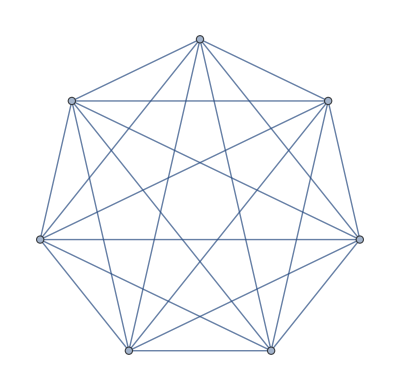
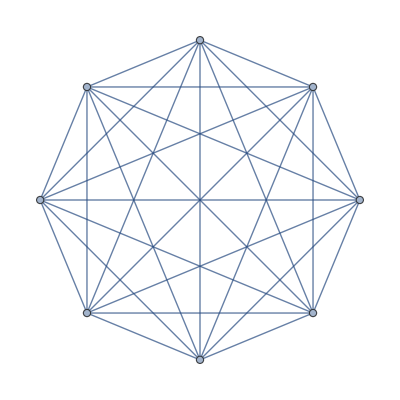
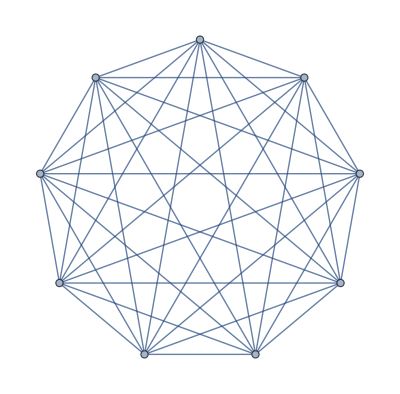

```mathematica
Table[CompleteGraph[i],{i,9}]
```


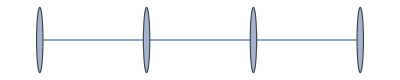
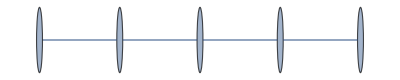
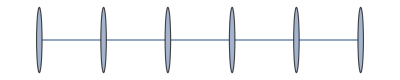
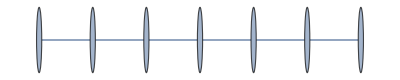
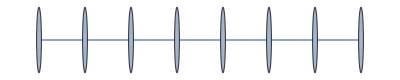
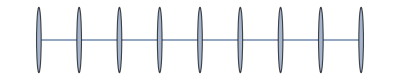
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PathGraph[Range[i]],{i,9}]
```

I’ll use the new isomorphism functionality introduced in recent releases of Mathematica:

```mathematica
FindGraphIsomorphism[-Graphics-,-Graphics-]
```

{<|1→1|>}

```mathematica
Names["*Isom*"]
```

{FindGraphIsomorphism,FindIsomers,FindIsomorphicSubgraph,FindSubgraphIsomorphism,IsomorphicGraphQ,IsomorphicSubgraphQ}

```mathematica
Information/@Names["*Isom*"]
```

{,,,,,}

```mathematica
Select[IsomorphicGraphQ[CompleteGraph[#],PathGraph[Range[#]]]&][Range[10]]
```

{1,2}

```mathematica
Select[IsomorphicGraphQ[CompleteGraph[#],CycleGraph[#]]&][Range[10]]
```

{3}

Donald Knuth lists 0 as an answer as well in addition to 3, but I don’t think the 0 graph exists or makes sense.

## Exercise 43

Are any of the following graphs the same as the Petersen graph?

I have a hard copy edition of the Art of Computer Programming that I am using to answer this exercise.

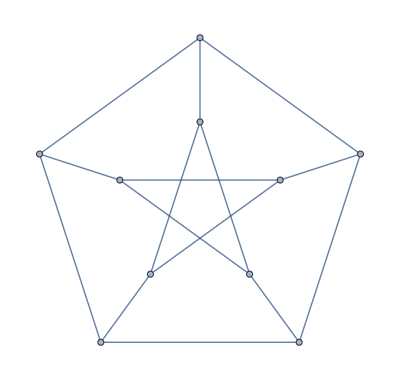

```mathematica
GraphData["PetersenGraph"]
```

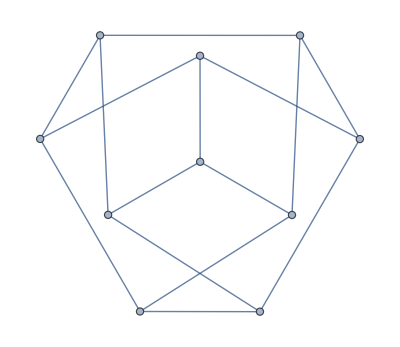

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,1<->5,9<->1,2<->7,3<->10,9<->10,6<->10,4<->8}]
```

```mathematica
IsomorphicGraphQ[Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,1<->5,9<->1,2<->7,3<->10,9<->10,6<->10,4<->8}],GraphData["PetersenGraph"]]
```

True

```mathematica
FindGraphIsomorphism[Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,1<->5,9<->1,2<->7,3<->10,9<->10,6<->10,4<->8}],GraphData["PetersenGraph"]]
```

{<|1→1,2→4,3→2,4→5,5→3,6→8,7→9,8→10,9→6,10→7|>}

```mathematica
GraphData["PetersenGraph","Embeddings"]
```

{{{0.,1.},{-0.951,0.309},{-0.588,-0.809},{0.588,-0.809},{0.951,0.309},{0.,2.},{-1.902,0.618},{-1.176,-1.618},{1.176,-1.618},{1.902,0.618}},{{0.323,0.975},{0.037,0.789},{0.037,0.186},{0.323,0.},{0.5,0.487},{1.287,0.975},{1.,0.789},{1.,0.186},{1.287,0.},{1.464,0.487}},{{0.448354,-0.269958},{0.60481,-0.338987},{0.586329,-0.50903},{0.586329,-0.0309114},{0.862447,-0.50903},{0.724304,-0.131983},{0.724304,-0.269958},{0.843797,-0.338987},{0.862447,-0.0309114},{1.,-0.269958}},{{0.448354,-0.269958},{0.606498,-0.145654},{0.529114,-0.0747932},{0.529114,-0.465148},{0.84211,-0.145654},{1.,-0.269958},{0.919831,-0.0747932},{0.724304,0.00606582},{0.724304,-0.545992},{0.919831,-0.465148}},{{0.454407,-0.222966},{0.632542,-0.53161},{0.549237,-0.0587373},{0.487373,-0.409661},{0.822119,-0.53161},{1.,-0.222966},{0.905932,-0.0587373},{0.727373,0.00609153},{0.727373,-0.271102},{0.967797,-0.409661}},{{0.602252,-0.541848},{0.734705,-0.312345},{0.668478,-0.656599},{0.668478,-0.427096},{0.867236,-0.312345},{1.,-0.541848},{0.93323,-0.656599},{0.801242,-0.656599},{0.801242,-0.503571},{0.93323,-0.427096}},{{0,0},{1,3},{0,4},{1,1},{4,4},{2,0},{2,2},{3,3},{3,1},{4,0}},{{2,2},{6,4},{4,2},{2,4},{6,2},{5,5},{6,6},{4,6},{2,6},{3,5}},{{√(2/(5+√5)),0},{1/2 √(1-2/(√5)),1/2},{-1/2 √(1/10 (5+√5)),1/4 (-1+√5)},{-1/2 √(1/10 (5+√5)),1/4 (1-√5)},{1/2 √(1-2/(√5)),-1/2},{0,√(1/10 (5+√5))},{1/4 (-1-√5),1/2 √(1/10 (5-√5))},{-1/2,-1/2 √(1+2/(√5))},{1/2,-1/2 √(1+2/(√5))},{1/4 (1+√5),1/2 √(1/10 (5-√5))}},{{0.535302,0.95889},{0.328164,0.677274},{0.535302,0.470135},{0.0706049,0.621205},{0.328164,0.262996},{1.,0.621205},{0.742441,0.677274},{0.742441,0.262996},{0.247912,0.0745965},{0.822693,0.0745965}},{{√(5/8-(√5)/8),1/4 (-1-√5)},{0,1},{√(1/2 (5-√5)),1/2 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,2},{-1/2 √(1/2 (5-√5)),1/4 (-1-√5)},{-1/2 √(1/2 (5+√5)),1/4 (-1+√5)},{-√(1/2 (5+√5)),1/2 (-1+√5)},{√(1/2 (5+√5)),1/2 (-1+√5)},{-√(1/2 (5-√5)),1/2 (-1-√5)}}}

```mathematica
Length[GraphData["PetersenGraph","Embeddings"]]
```

11

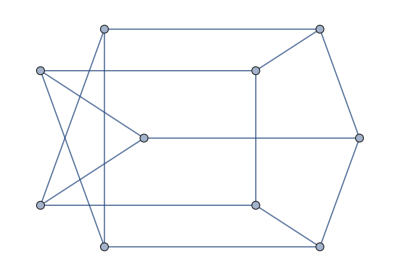
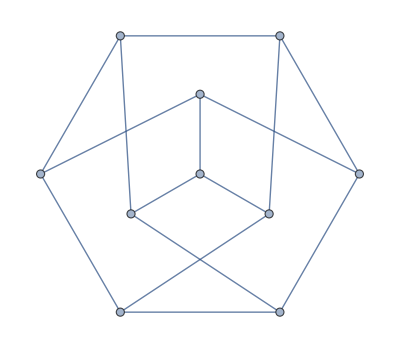
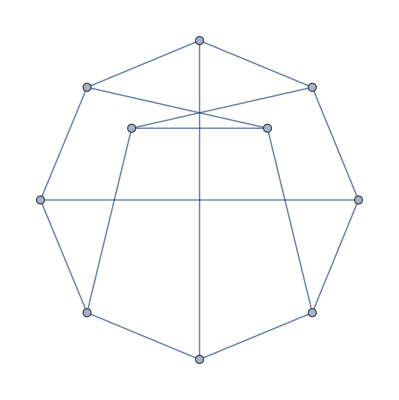
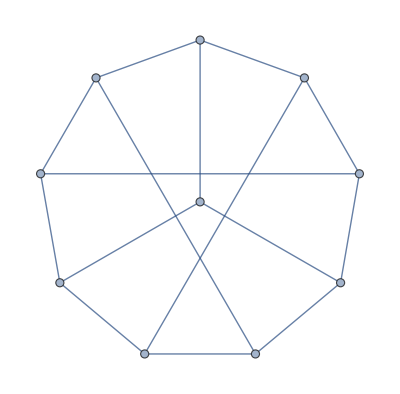
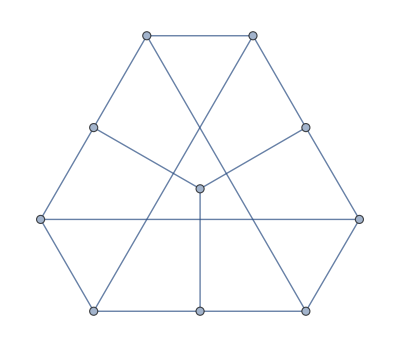
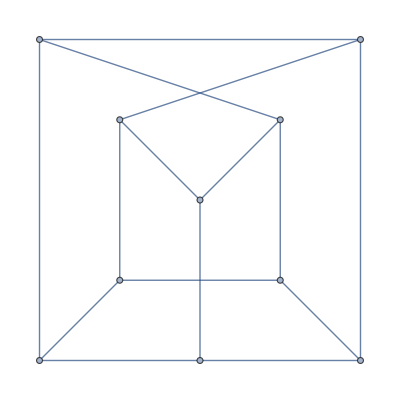
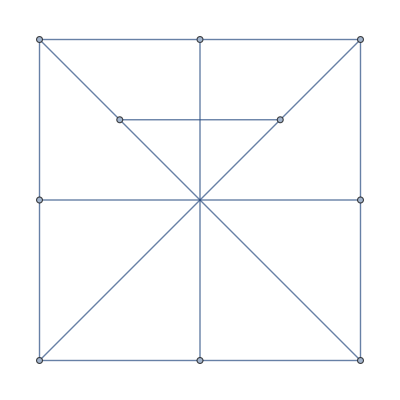
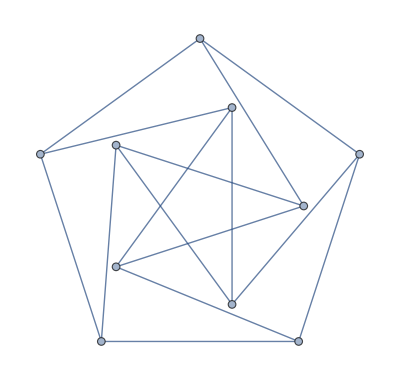
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph[GraphData["PetersenGraph"],VertexCoordinates->#]&/@GraphData["PetersenGraph","Embeddings"]
```

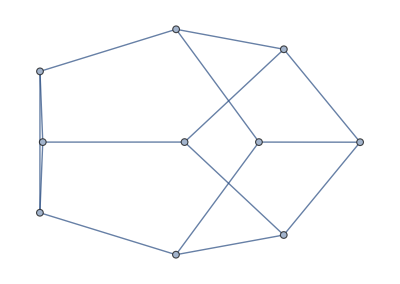

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,1<->7,3<->7,5<->7,2<->8,4<->9,6<->10,8<->9,9<->10,8<->10}]
```

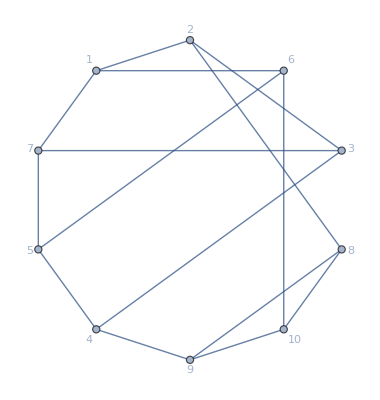

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,1<->7,3<->7,5<->7,2<->8,4<->9,6<->10,8<->9,9<->10,8<->10},GraphLayout->"CircularEmbedding",VertexLabels->Automatic]
```

```mathematica
IsomorphicGraphQ[Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,1<->7,3<->7,5<->7,2<->8,4<->9,6<->10,8<->9,9<->10,8<->10},GraphLayout->"CircularEmbedding",VertexLabels->Automatic],GraphData["PetersenGraph"]]
```

False

```mathematica
FindGraphIsomorphism[GraphData["PetersenGraph"],-Graphics-]
```

{<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>}

```mathematica
FindGraphIsomorphism[GraphData["PetersenGraph"],-Graphics-]
```

```mathematica
FindGraphIsomorphism[GraphData["PetersenGraph"],-Graphics-]
```

{<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>}

```mathematica
FindGraphIsomorphism[-Graphics-,GraphData["PetersenGraph"]]
```

{<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>}

## Exercise 44

How many symmetries does Chvàtal’s graph have?

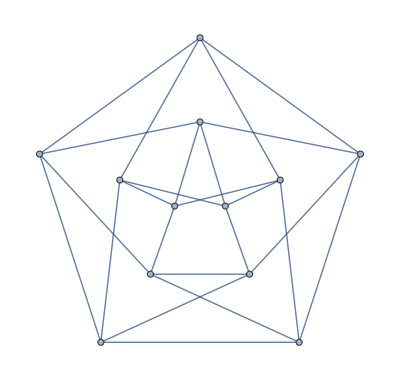

```mathematica
GraphData["ChvatalGraph"]
```

```mathematica
GraphData["ChvatalGraph","AutomorphismCount"]
```

8

There are 8 symmetries.

## Exercise 45

Find an easy way to 4-color the planar graph (17). Would 3 colors suffice?

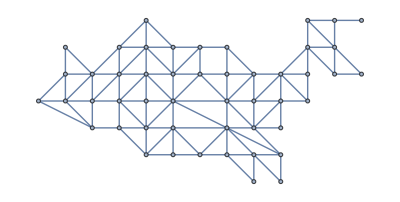

```mathematica
GraphData["ContiguousUSAGraph"]
```

```mathematica
VertexCount[GraphData["ContiguousUSAGraph"]]
```

49

```mathematica
GraphData["ContiguousUSAGraph","ChromaticNumber"]
```

4

The minimum number of colors possible is 4.

```mathematica
FindVertexColoring[GraphData["ContiguousUSAGraph"]]
```

{3,1,2,2,1,3,1,2,1,2,2,4,3,3,1,1,2,3,1,3,3,2,1,1,1,3,2,1,3,2,3,1,3,1,1,2,2,2,1,3,2,3,1,4,1,1,3,2,3}

I can use a resource function I created to color a graph:

```mathematica
ResourceSearch["*color*graph*"]
```

```mathematica
PersistResourceFunction[{"ColorGraphVertices"}]
```

{Success[…]}

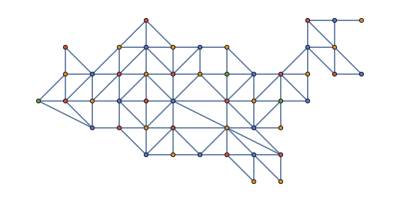

```mathematica
ColorGraphVertices[GraphData["ContiguousUSAGraph"]]
```

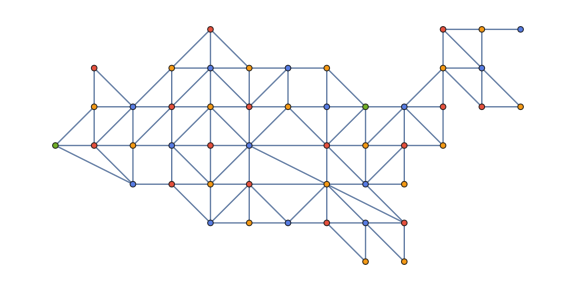

```mathematica
ColorGraphVertices[GraphData["ContiguousUSAGraph"],ImageSize->Large]
```

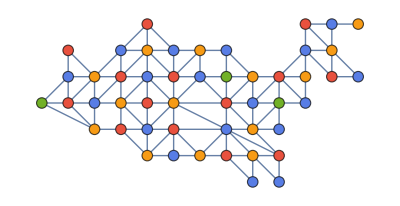

```mathematica
ColorGraphVertices[GraphData["ContiguousUSAGraph"],ImageSize->Full,VertexSize->Large]
```

## Exercise 46

Let G with a graph with n>=3 vertices, defined by a planar diagram that is “maximal,” in the sense that no additional lines can be drawn between nonadjacent vertices without crossing an existing edge.

The graph data property I am looking for is “Triangulated” or “maximally planar”.

```mathematica
GraphData["Triangulated"]
```

{{Apollonian,2},{Apollonian,3},{Apollonian,4},{Apollonian,5},{Apollonian,6},{ChromaticallyEquivalent,{11,1,1}},{ChromaticallyEquivalent,{11,1,2}},{ChromaticallyEquivalent,{11,2,1}},{ChromaticallyEquivalent,{11,2,2}},{ChromaticallyEquivalent,{11,3,1}},{ChromaticallyEquivalent,{11,3,2}},{ChromaticallyEquivalent,{12,1,1}},{ChromaticallyEquivalent,{12,1,2}},{ChromaticallyEquivalent,{13,1,1}},{ChromaticallyEquivalent,{13,1,2}},{ChromaticallyEquivalent,{13,1,3}},{ChromaticallyEquivalent,{13,2,1}},{ChromaticallyEquivalent,{13,2,2}},{ChromaticallyEquivalent,{14,1,1}},{ChromaticallyEquivalent,{14,1,2}},{ChromaticallyEquivalent,{14,2,1}},{ChromaticallyEquivalent,{14,2,2}},{ChromaticallyEquivalent,{14,3,1}},{ChromaticallyEquivalent,{14,3,2}},{ChromaticallyEquivalent,{14,4,1}},{ChromaticallyEquivalent,{14,4,2}},{ChromaticallyEquivalent,{15,1,1}},{ChromaticallyEquivalent,{15,1,2}},{ChromaticallyEquivalent,{15,1,3}},{ChromaticallyEquivalent,{15,2,1}},{ChromaticallyEquivalent,{15,2,2}},{ChromaticallyEquivalent,{15,3,1}},{ChromaticallyEquivalent,{15,3,2}},{ChromaticallyEquivalent,{15,4,1}},{ChromaticallyEquivalent,{15,4,2}},{ChromaticallyEquivalent,{15,5,1}},{ChromaticallyEquivalent,{15,5,2}},{ChromaticallyEquivalent,{15,6,1}},{ChromaticallyEquivalent,{15,6,2}},{ChromaticallyEquivalent,{16,1,1}},{ChromaticallyEquivalent,{16,1,2}},{ChromaticallyEquivalent,{16,2,1}},{ChromaticallyEquivalent,{16,2,2}},{ChromaticallyEquivalent,{16,3,1}},{ChromaticallyEquivalent,{16,3,2}},{ChromaticallyEquivalent,{16,4,1}},{ChromaticallyEquivalent,{16,4,2}},{ChromaticallyEquivalent,{16,5,1}},{ChromaticallyEquivalent,{16,5,2}},{ChromaticallyEquivalent,{16,6,1}},{ChromaticallyEquivalent,{16,6,2}},{ChromaticallyEquivalent,{16,7,1}},{ChromaticallyEquivalent,{16,7,2}},{ChromaticallyEquivalent,{16,8,1}},{ChromaticallyEquivalent,{16,8,2}},{ChromaticallyEquivalent,{16,9,1}},{ChromaticallyEquivalent,{16,9,2}},{ChromaticallyEquivalent,{17,1,1}},{ChromaticallyEquivalent,{17,1,2}},{Dipyramid,3},{Dipyramid,5},{Dipyramid,6},{Dipyramid,7},{Dipyramid,8},{Dipyramid,9},{Dipyramid,10},{Dipyramid,11},{Dipyramid,12},{Dipyramid,13},{Dipyramid,14},{Dipyramid,15},{Dipyramid,16},{Dipyramid,17},{Dipyramid,18},{Dipyramid,19},{Dipyramid,20},DisdyakisDodecahedralGraph,DisdyakisTriacontahedralGraph,ErreraGraph,FritschGraph,GoldnerHararyGraph,HeawoodFourColorGraph,{Heptahedral,15},{Heptahedral,29},{Heptahedral,34},{Hexahedral,5},IcosahedralGraph,{JohnsonSkeleton,17},{JohnsonSkeleton,84},KittellGraph,McGregorGraph,MooreGraph,OctahedralGraph,PentakisDodecahedralGraph,PentakisIcosidodecahedralGraph,PoussinGraph,{SierpinskiTetrahedron,2},SmallTriakisOctahedralGraph,TetrahedralGraph,TetrakisHexahedralGraph,TriakisIcosahedralGraph,TriakisTetrahedralGraph,TriangleGraph,{Triangulated,{8,2}},{Triangulated,{8,3}},{Triangulated,{8,4}},{Triangulated,{8,5}},{Triangulated,{8,6}},{Triangulated,{8,8}},{Triangulated,{8,9}},{Triangulated,{8,10}},{Triangulated,{8,11}},{Triangulated,{8,12}},{Triangulated,{8,14}}}

Prove that the diagram partitions the plane into regions that each have exactly three vertices on their boundary. (One of these regions is the set of all points that lie outside the diagram.)

Therefore G has exactly 3n-6 edges.

I think there’s a graph function that does something with a plane.

```mathematica
Names["*plan*",IgnoreCase->True]
```

{ClipPlanes,ClipPlanesStyle,CoplanarPoints,DualPlanarGraph,ExoplanetData,FindPlanarColoring,HalfPlane,Hyperplane,InfinitePlane,MinorPlanetData,PlanarAngle,PlanarFaceList,PlanarGraph,PlanarGraphQ,PlanckRadiationLaw,PlaneCurveData,PlanetaryMoonData,PlanetData,PlantData,PlotRangeClipPlanesStyle}

```mathematica
Information/@Names["*plan*",IgnoreCase->True]
```

```mathematica
{,,,,}
```

Select graphs with at least three vertices:

I was running this in 13.2 but I got an error so I had to evaluate it in 13.1.

This is the error in 13.2

```mathematica
$Version
```

13.2.0 for Microsoft Windows (64-bit) (November 6, 2022)

```mathematica
triangulatedGraphsWithAtLastThreeVertices=Select[VertexCount[GraphData[#]]>=3&][GraphData["Triangulated"]]
```

AdjacencyGraph::matsq: Argument If[{10-graph 12002618}>100,GraphLayout→None,Sequence@@{}] at position 2 is not a non-empty square matrix.

VertexCount::graph: A graph object is expected at position 1 in VertexCount[AdjacencyGraph[{{10,12002618}},If[{10-graph 12002618}>100,GraphLayout→None,Sequence@@{}]]].

{{Apollonian,2},{Apollonian,3},{Apollonian,4},{Apollonian,5},{Apollonian,6},{ChromaticallyEquivalent,{11,1,1}},{ChromaticallyEquivalent,{11,1,2}},{ChromaticallyEquivalent,{11,2,1}},{ChromaticallyEquivalent,{11,2,2}},{ChromaticallyEquivalent,{11,3,1}},{ChromaticallyEquivalent,{11,3,2}},{ChromaticallyEquivalent,{12,1,1}},{ChromaticallyEquivalent,{12,1,2}},{ChromaticallyEquivalent,{13,1,1}},{ChromaticallyEquivalent,{13,1,2}},{ChromaticallyEquivalent,{13,1,3}},{ChromaticallyEquivalent,{13,2,1}},{ChromaticallyEquivalent,{13,2,2}},{ChromaticallyEquivalent,{14,1,1}},{ChromaticallyEquivalent,{14,1,2}},{ChromaticallyEquivalent,{14,2,1}},{ChromaticallyEquivalent,{14,2,2}},{ChromaticallyEquivalent,{14,3,1}},{ChromaticallyEquivalent,{14,3,2}},{ChromaticallyEquivalent,{14,4,1}},{ChromaticallyEquivalent,{14,4,2}},{ChromaticallyEquivalent,{15,1,1}},{ChromaticallyEquivalent,{15,1,2}},{ChromaticallyEquivalent,{15,1,3}},{ChromaticallyEquivalent,{15,2,1}},{ChromaticallyEquivalent,{15,2,2}},{ChromaticallyEquivalent,{15,3,1}},{ChromaticallyEquivalent,{15,3,2}},{ChromaticallyEquivalent,{15,4,1}},{ChromaticallyEquivalent,{15,4,2}},{ChromaticallyEquivalent,{15,5,1}},{ChromaticallyEquivalent,{15,5,2}},{ChromaticallyEquivalent,{15,6,1}},{ChromaticallyEquivalent,{15,6,2}},{ChromaticallyEquivalent,{16,1,1}},{ChromaticallyEquivalent,{16,1,2}},{ChromaticallyEquivalent,{16,2,1}},{ChromaticallyEquivalent,{16,2,2}},{ChromaticallyEquivalent,{16,3,1}},{ChromaticallyEquivalent,{16,3,2}},{ChromaticallyEquivalent,{16,4,1}},{ChromaticallyEquivalent,{16,4,2}},{ChromaticallyEquivalent,{16,5,1}},{ChromaticallyEquivalent,{16,5,2}},{ChromaticallyEquivalent,{16,6,1}},{ChromaticallyEquivalent,{16,6,2}},{ChromaticallyEquivalent,{16,7,1}},{ChromaticallyEquivalent,{16,7,2}},{ChromaticallyEquivalent,{16,8,1}},{ChromaticallyEquivalent,{16,8,2}},{ChromaticallyEquivalent,{16,9,1}},{ChromaticallyEquivalent,{16,9,2}},{ChromaticallyEquivalent,{17,1,1}},{ChromaticallyEquivalent,{17,1,2}},{Dipyramid,3},{Dipyramid,5},{Dipyramid,6},{Dipyramid,7},{Dipyramid,8},{Dipyramid,9},{Dipyramid,10},{Dipyramid,11},{Dipyramid,12},{Dipyramid,13},{Dipyramid,14},{Dipyramid,15},{Dipyramid,16},{Dipyramid,17},{Dipyramid,18},{Dipyramid,19},{Dipyramid,20},DisdyakisDodecahedralGraph,DisdyakisTriacontahedralGraph,ErreraGraph,FritschGraph,GoldnerHararyGraph,HeawoodFourColorGraph,{Heptahedral,15},{Heptahedral,29},{Heptahedral,34},{Hexahedral,5},IcosahedralGraph,{JohnsonSkeleton,17},{JohnsonSkeleton,84},KittellGraph,McGregorGraph,MooreGraph,OctahedralGraph,PentakisDodecahedralGraph,PentakisIcosidodecahedralGraph,PoussinGraph,{SierpinskiTetrahedron,2},SmallTriakisOctahedralGraph,TetrahedralGraph,TetrakisHexahedralGraph,TriakisIcosahedralGraph,TriakisTetrahedralGraph,{Triangulated,{8,2}},{Triangulated,{8,3}},{Triangulated,{8,4}},{Triangulated,{8,5}},{Triangulated,{8,6}},{Triangulated,{8,8}},{Triangulated,{8,9}},{Triangulated,{8,10}},{Triangulated,{8,11}},{Triangulated,{8,12}},{Triangulated,{8,14}}}

This is the evaluation in 13.1

```mathematica
$Version
```

13.1.0 for Microsoft Windows (64-bit) (June 16, 2022)

```mathematica
triangulatedGraphsWithAtLastThreeVertices=Select[VertexCount[GraphData[#]]>=3&][GraphData["Triangulated"]]
```

{{Apollonian,2},{Apollonian,3},{Apollonian,4},{Apollonian,5},{Apollonian,6},{ChromaticallyEquivalent,{11,1,1}},{ChromaticallyEquivalent,{11,1,2}},{ChromaticallyEquivalent,{11,2,1}},{ChromaticallyEquivalent,{11,2,2}},{ChromaticallyEquivalent,{11,3,1}},{ChromaticallyEquivalent,{11,3,2}},{ChromaticallyEquivalent,{12,1,1}},{ChromaticallyEquivalent,{12,1,2}},{ChromaticallyEquivalent,{13,1,1}},{ChromaticallyEquivalent,{13,1,2}},{ChromaticallyEquivalent,{13,1,3}},{ChromaticallyEquivalent,{13,2,1}},{ChromaticallyEquivalent,{13,2,2}},{ChromaticallyEquivalent,{14,1,1}},{ChromaticallyEquivalent,{14,1,2}},{ChromaticallyEquivalent,{14,2,1}},{ChromaticallyEquivalent,{14,2,2}},{ChromaticallyEquivalent,{14,3,1}},{ChromaticallyEquivalent,{14,3,2}},{ChromaticallyEquivalent,{14,4,1}},{ChromaticallyEquivalent,{14,4,2}},{ChromaticallyEquivalent,{15,1,1}},{ChromaticallyEquivalent,{15,1,2}},{ChromaticallyEquivalent,{15,1,3}},{ChromaticallyEquivalent,{15,2,1}},{ChromaticallyEquivalent,{15,2,2}},{ChromaticallyEquivalent,{15,3,1}},{ChromaticallyEquivalent,{15,3,2}},{ChromaticallyEquivalent,{15,4,1}},{ChromaticallyEquivalent,{15,4,2}},{ChromaticallyEquivalent,{15,5,1}},{ChromaticallyEquivalent,{15,5,2}},{ChromaticallyEquivalent,{15,6,1}},{ChromaticallyEquivalent,{15,6,2}},{ChromaticallyEquivalent,{16,1,1}},{ChromaticallyEquivalent,{16,1,2}},{ChromaticallyEquivalent,{16,2,1}},{ChromaticallyEquivalent,{16,2,2}},{ChromaticallyEquivalent,{16,3,1}},{ChromaticallyEquivalent,{16,3,2}},{ChromaticallyEquivalent,{16,4,1}},{ChromaticallyEquivalent,{16,4,2}},{ChromaticallyEquivalent,{16,5,1}},{ChromaticallyEquivalent,{16,5,2}},{ChromaticallyEquivalent,{16,6,1}},{ChromaticallyEquivalent,{16,6,2}},{ChromaticallyEquivalent,{16,7,1}},{ChromaticallyEquivalent,{16,7,2}},{ChromaticallyEquivalent,{16,8,1}},{ChromaticallyEquivalent,{16,8,2}},{ChromaticallyEquivalent,{16,9,1}},{ChromaticallyEquivalent,{16,9,2}},{ChromaticallyEquivalent,{17,1,1}},{ChromaticallyEquivalent,{17,1,2}},{Dipyramid,3},{Dipyramid,5},{Dipyramid,6},{Dipyramid,7},{Dipyramid,8},{Dipyramid,9},{Dipyramid,10},{Dipyramid,11},{Dipyramid,12},{Dipyramid,13},{Dipyramid,14},{Dipyramid,15},{Dipyramid,16},{Dipyramid,17},{Dipyramid,18},{Dipyramid,19},{Dipyramid,20},DisdyakisDodecahedralGraph,DisdyakisTriacontahedralGraph,ErreraGraph,FritschGraph,GoldnerHararyGraph,HeawoodFourColorGraph,{Heptahedral,15},{Heptahedral,29},{Heptahedral,34},{Hexahedral,5},IcosahedralGraph,{JohnsonSkeleton,17},{JohnsonSkeleton,84},KittellGraph,McGregorGraph,MooreGraph,OctahedralGraph,PentakisDodecahedralGraph,PoussinGraph,{SierpinskiTetrahedron,2},SmallTriakisOctahedralGraph,TetrahedralGraph,TetrakisHexahedralGraph,TriakisIcosahedralGraph,TriakisTetrahedralGraph,TriangleGraph,{Triangulated,{8,2}},{Triangulated,{8,3}},{Triangulated,{8,4}},{Triangulated,{8,5}},{Triangulated,{8,6}},{Triangulated,{8,8}},{Triangulated,{8,9}},{Triangulated,{8,10}},{Triangulated,{8,11}},{Triangulated,{8,12}},{Triangulated,{8,14}}}

```mathematica
PlanarFaceList[GraphData[#]]&/@triangulatedGraphsWithAtLastThreeVertices
```

I am going to work on creating a function to make a planar coloring. I used the code from ColorGraphEdges to build a new function ColorPlanarGraphFaces.

```mathematica
ResourceFunction["ResourceFunctionDefinitionViewer"]["ColorGraphEdges"]
```

Here is an example:

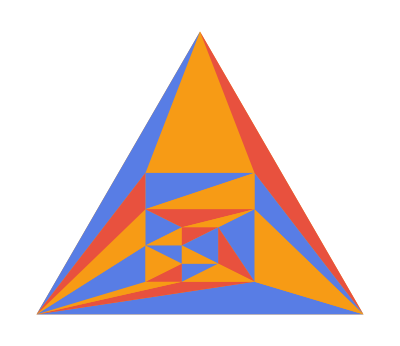

```mathematica
ResourceFunction[CloudObject["https://www.wolframcloud.com/obj/burbery1/DeployedResources/Function/ColorPlanarGraphFaces"]][GraphData[{"ChromaticallyEquivalent",{16,6,1}}]]
```

I can compare the number of vertices n with the number of edges which should be 3n-6.

```mathematica
AllTrue[triangulatedGraphsWithAtLastThreeVertices,3VertexCount[GraphData[#]]-6==EdgeCount[GraphData[#]]&]
```

True

This is true for all graphs.

## Exercise 47

Prove that the complete bigraph K_(3,3) isn’t planar.

This is related to the famous three utilities problem. It is well-known that you connect three houses to each other so each one has water, gas, and electricity. This means the complete bipartite graph K_(3,3) is not planar and cannot be embedded in the plane. This graph can however, be embedded on a torus. The toroidal embedding of this graph could be used to create a solution to the three utilities on a torus or donut or coffee cup or tire or other object that topologically homeomorphic to a torus.

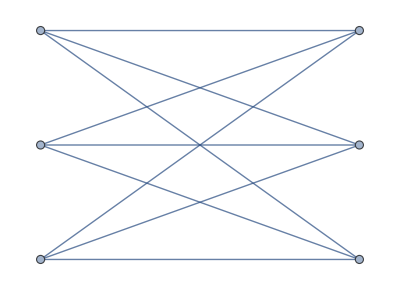

```mathematica
CompleteGraph[{3,3}]
```

```mathematica
PlanarGraphQ[CompleteGraph[{3,3}]]
```

False

Find the canonical graph:

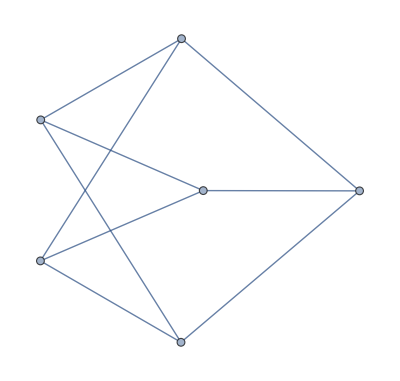

```mathematica
CanonicalGraph[CompleteGraph[{3,3}]]
```

Find the name of the graph data entry:

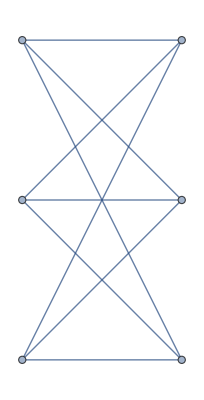

```mathematica
GraphData[{"CompleteBipartite", {3, 3}}]
```

Verify the graphs are isomorphic:

```mathematica
IsomorphicGraphQ[GraphData[{"CompleteBipartite", {3, 3}}],CompleteGraph[{3,3}]]
```

True

```mathematica
GraphData[{"CompleteBipartite",{3,3}},"Planar"]
```

False

The property apices is the list of vertices whose removal renders the graph planar:

```mathematica
GraphData[{"CompleteBipartite",{3,3}},"Apices"]
```

{1,2,3,4,5,6}

## Exercise 25

Complete the proof of Theorem B by showing that the stated procedure never the same color to two adjacent vertices.

Theorem B: A graph is bipartite if and only if it contains no cycle of odd length.

Conversely, if a graph contains no odd cycles we can color its vertices with the two colors {0,1} by carrying out the following procedure: Begin with all vertices uncolored. If all neighbors of colored vertices are already colored, choose an uncolored vertex w, and color it 0. Otherwise choose a colored vertex u that has an uncolored neighbor v; assign to v the opposite color. Exercise 48 proves that a valid 2-coloring is eventually obtained.

I will use examples to demonstrate a case for this.

```mathematica
GraphData["Bipartite"]
```

I will verify that all bipartite graphs have a chromatic number of two.

```mathematica
AllTrue[GraphData["Bipartite"],GraphData[#,"ChromaticNumber"]==2&]
```